## Brian — PS 2 — 2025-01-21 — Solution

## EIWL3 Sections 5-8

## Exercises from EIWL3 Section 5

```mathematica
(* 5.1 *) Reverse[Range[10]^2] (* I could square and reverse or reverse and square. *)
```

{100,81,64,49,36,25,16,9,4,1}

```mathematica
(* 5.2 *) Total[Reverse[Range[3]]^2]
```

14

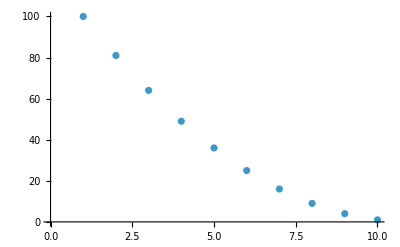

```mathematica
(* 5.3 *) ListPlot[Reverse[Range[10]]^2 ]
```

```mathematica
(* 5.4 *) Sort[Join[Range[4],Range[4]]]
```

{1,1,2,2,3,3,4,4}

```mathematica
(* 5.5 *) Range[10,20,1] (* Range[10, 20, 1] is simpler and clearer but it isn't what Wolfram requested us to do. *)
```

{10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Range[11] + 9 (* This way uses Plus as Wolfram requested *)
```

```mathematica
(* 5.6 *) Sort[Join[Range[5]^2, Range[5]^3]]
```

{1,1,4,8,9,16,25,27,64,125}

```mathematica
(* 5.7 *) Length[IntegerDigits[2^128]]
```

39

```mathematica
(* 5.8 *) First[IntegerDigits[2^32]]
```

4

```mathematica
(* 5.9 *) Take[IntegerDigits[2^100],10]
```

{1,2,6,7,6,5,0,6,0,0}

```mathematica
(* 5.10 *) Max[IntegerDigits[2^20]]
```

8

```mathematica
(* 5.11 *) Count[IntegerDigits[2^1000],0]
```

28

```mathematica
(* 5.12 *) Sort[IntegerDigits[2^20]][[0]] (* I am using a special notation for Part *)
```

List

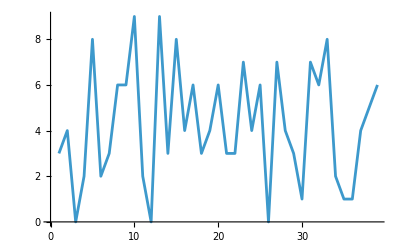

```mathematica
(* 5.13 *) ListLinePlot[IntegerDigits[2^128]]
```

```mathematica
(* 5.14 *) Drop[Take[Range[100],20],10]
```

{11,12,13,14,15,16,17,18,19,20}

## Exercises from EIWL3 Section 6

```mathematica
(* 6.1 *) Table[1000,5]
```

{1000,1000,1000,1000,1000}

```mathematica
(* 6.2 *) Table[n^3,{n,10,20}]
```

{1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000}

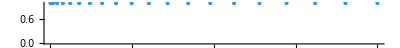

```mathematica
(* 6.3 *) NumberLinePlot[Table[n^2,{n,20}]]
```

```mathematica
(* 6.4 *) Table[i,{i,2,20,2}] (* I assume he wants to use Table with steps, but there are lots of other ways of doing this. E.g., *)
```

```mathematica
Table[i,{i,10}]2
```

{2,4,6,8,10,12,14,16,18,20}

```mathematica
(* 6.5 *) Table[i,{i,10}]
```

{1,2,3,4,5,6,7,8,9,10}

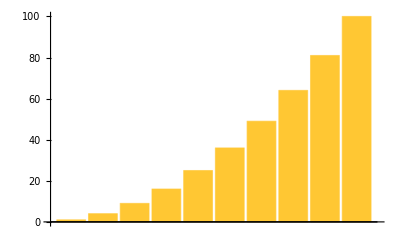

```mathematica
(* 6.6 *) BarChart[Table[i^2,{i,10}]]
```

```mathematica
(* 6.7 *) Table[IntegerDigits[i^2],{i,10}]
```

{{1},{4},{9},{1,6},{2,5},{3,6},{4,9},{6,4},{8,1},{1,0,0}}

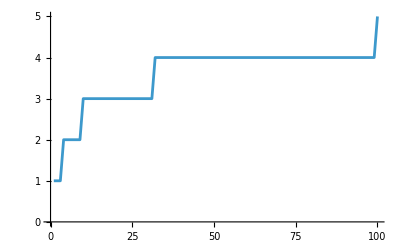

```mathematica
(* 6.8 *) ListLinePlot[Table[Length[IntegerDigits[i^2]],{i,100}]]
```

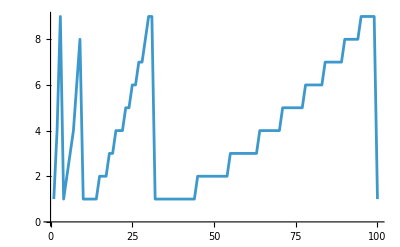

```mathematica
(* 6.8 *) ListLinePlot[Table[First[IntegerDigits[i^2]],{i,100}]]
```

```mathematica
(* 6.9 *)Table[First[IntegerDigits[i^2]],{i,20}]
```

{1,4,9,1,2,3,4,6,8,1,1,1,1,1,2,2,2,3,3,4}

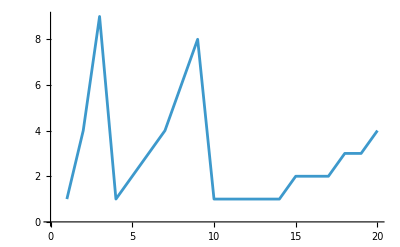

```mathematica
(* 6.10 *) ListLinePlot[Table[First[IntegerDigits[i^2]],{i,20}]]
```

## Exercises from EIWL3 Section 7

```mathematica
(* 7.1 *) {Red,Yellow,Green}
```

{RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0]}

```mathematica
(* 7.2 *) Column[{Red,Yellow,Green}]
```

RGBColor[1, 0, 0]
RGBColor[1, 1, 0]
RGBColor[0, 1, 0]

```mathematica
(* 7.3 *) ColorNegate[Orange]
```

RGBColor[0., 0.5, 1.]

```mathematica
(* 7.4 *) Table[Hue[i],{i,0,1,0.02}]
```

{Hue[0.],Hue[0.02],Hue[0.04],Hue[0.06],Hue[0.08],Hue[0.1],Hue[0.12],Hue[0.14],Hue[0.16],Hue[0.18],Hue[0.2],Hue[0.22],Hue[0.24],Hue[0.26],Hue[0.28],Hue[0.3],Hue[0.32],Hue[0.34],Hue[0.36],Hue[0.38],Hue[0.4],Hue[0.42],Hue[0.44],Hue[0.46],Hue[0.48],Hue[0.5],Hue[0.52],Hue[0.54],Hue[0.56],Hue[0.58],Hue[0.6],Hue[0.62],Hue[0.64],Hue[0.66],Hue[0.68],Hue[0.7000000000000001],Hue[0.72],Hue[0.74],Hue[0.76],Hue[0.78],Hue[0.8],Hue[0.8200000000000001],Hue[0.84],Hue[0.86],Hue[0.88],Hue[0.9],Hue[0.92],Hue[0.9400000000000001],Hue[0.96],Hue[0.98],Hue[1.]}

```mathematica
(* 7.5 *) Table[RGBColor[1.0,green,1.0],{green,0,1,0.05}]
```

{RGBColor[1., 0., 1.],RGBColor[1., 0.05, 1.],RGBColor[1., 0.1, 1.],RGBColor[1., 0.15000000000000002, 1.],RGBColor[1., 0.2, 1.],RGBColor[1., 0.25, 1.],RGBColor[1., 0.30000000000000004, 1.],RGBColor[1., 0.35000000000000003, 1.],RGBColor[1., 0.4, 1.],RGBColor[1., 0.45, 1.],RGBColor[1., 0.5, 1.],RGBColor[1., 0.55, 1.],RGBColor[1., 0.6000000000000001, 1.],RGBColor[1., 0.65, 1.],RGBColor[1., 0.7000000000000001, 1.],RGBColor[1., 0.75, 1.],RGBColor[1., 0.8, 1.],RGBColor[1., 0.8500000000000001, 1.],RGBColor[1., 0.9, 1.],RGBColor[1., 0.9500000000000001, 1.],RGBColor[1., 1., 1.]}

```mathematica
(* 7.6 *) Blend[{Pink,Yellow}]
```

RGBColor[1, 0.75, 0.25]

```mathematica
(* 7.7 *)Table[Blend[{Hue[i],Yellow}] ,{i,0,1,0.05}]
```

{RGBColor[1., 0.5, 0.],RGBColor[1., 0.65, 0.],RGBColor[1., 0.8, 0.],RGBColor[1., 0.9500000000000001, 0.],RGBColor[0.8999999999999999, 1., 0.],RGBColor[0.75, 1., 0.],RGBColor[0.5999999999999999, 1., 0.],RGBColor[0.5, 1., 0.050000000000000044],RGBColor[0.5, 1., 0.20000000000000018],RGBColor[0.5, 1., 0.3500000000000001],RGBColor[0.5, 1., 0.5],RGBColor[0.5, 0.8499999999999999, 0.5],RGBColor[0.5, 0.6999999999999997, 0.5],RGBColor[0.5, 0.5499999999999998, 0.5],RGBColor[0.6000000000000001, 0.5, 0.5],RGBColor[0.75, 0.5, 0.5],RGBColor[0.9000000000000004, 0.5, 0.5],RGBColor[1., 0.5, 0.44999999999999973],RGBColor[1., 0.5, 0.2999999999999998],RGBColor[1., 0.5, 0.1499999999999999],RGBColor[1., 0.5, 0.]}

```mathematica
(* 7.8 *) Table[Style[i,Hue[i]],{i,0.0,1.0,0.1}]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
(* 7.9 *) Style[Purple,100]
```

RGBColor[0.5, 0, 0.5]

```mathematica
(* 7.10 *) Table[Style[Red,i],{i,10,100,10}]
```

{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]}

```mathematica
(* 7.11 *) Style[999,Red,100]
```

999

```mathematica
(* 7.12 *) Table[Style[i,i],{i,Range[10]^2}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
(* 7.13 *) {Red,Yellow,Green}[[RandomInteger[2,100]+1]]
```

{RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0]}

```mathematica
(* 7.14 *) Table[Style[i,3i],{i,Take[IntegerDigits[2^1000],50]}]
```

{1,0,7,1,5,0,8,6,0,7,1,8,6,2,6,7,3,2,0,9,4,8,4,2,5,0,4,9,0,6,0,0,0,1,8,1,0,5,6,1,4,0,4,8,1,1,7,0,5,5}

## Exercises from EIWL3 Section 8



```mathematica
(* 8.1 *) Graphics[RegularPolygon[3]]
```

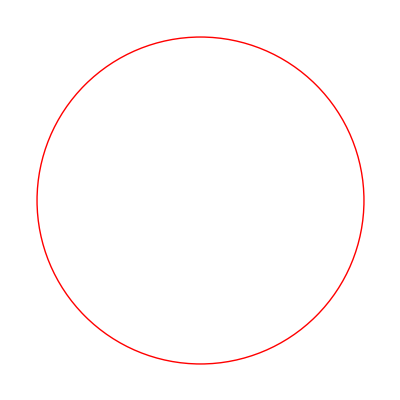

```mathematica
(* 8.2 *) Graphics[Style[Circle[],Red]]
```

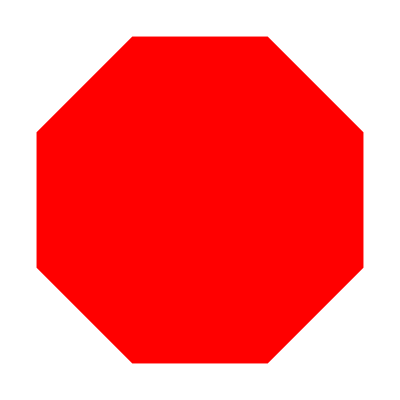

```mathematica
(* 8.3 *) Graphics[Style[RegularPolygon[8],Red]]
```


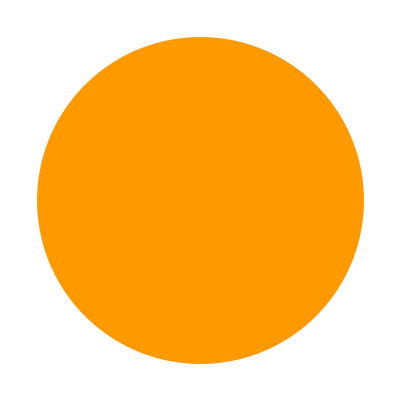
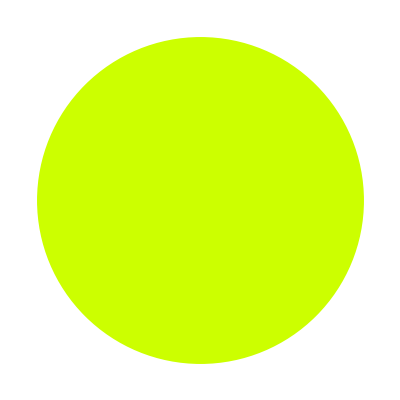
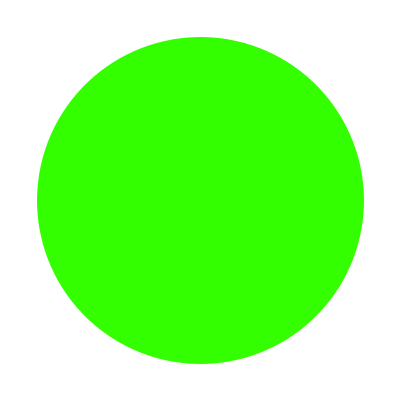
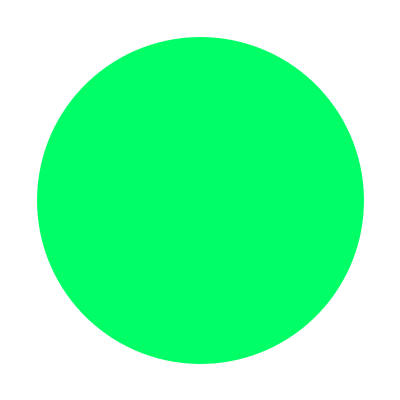
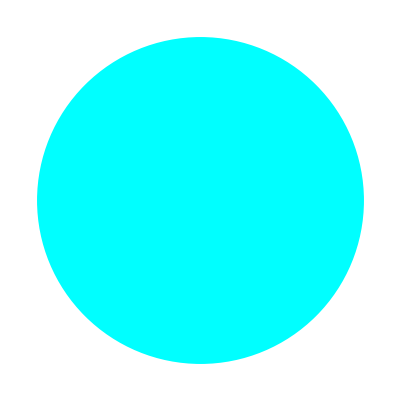
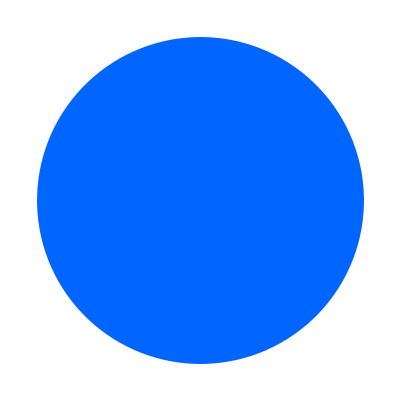
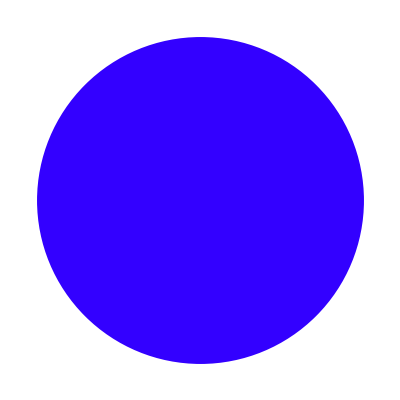
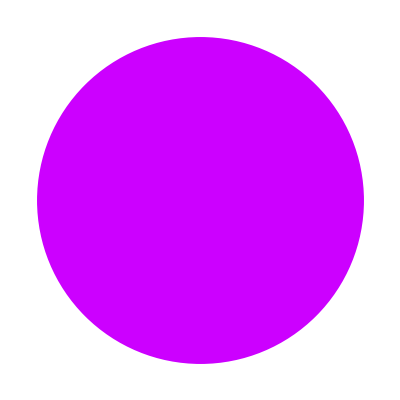
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* 8.4 *) Table[Graphics[Style[Disk[],Hue[i]]],{i,0.0,1.0,0.1}]
```

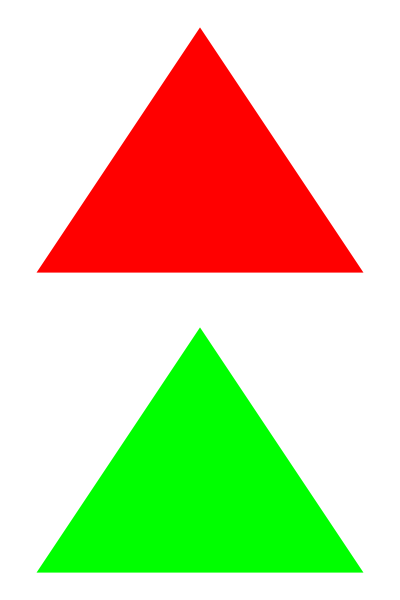

```mathematica
(* 8.5 *) Column[{
Graphics[Style[RegularPolygon[3],Red]],
Graphics[Style[RegularPolygon[3],Green]]
}] (* The nested brackets and braces got deep enough that I used indenting to help me get it right. *)
```

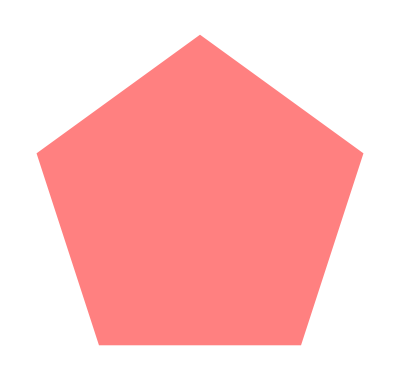
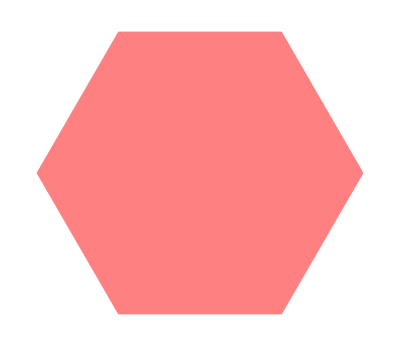
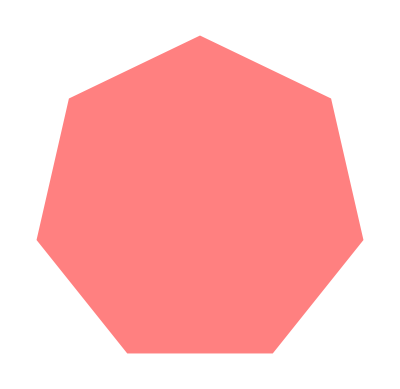
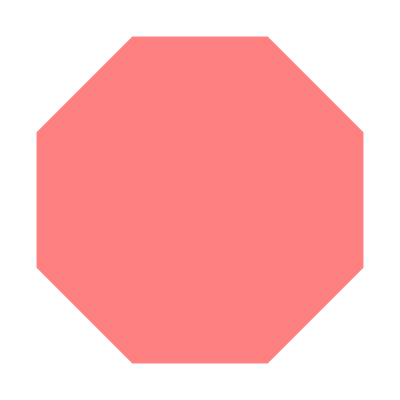
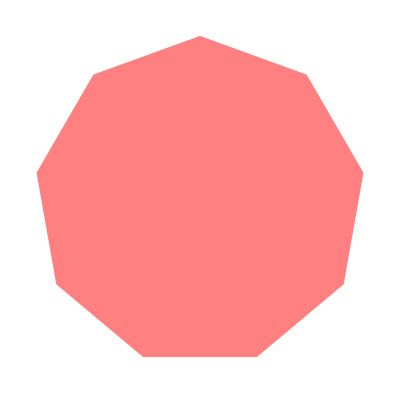
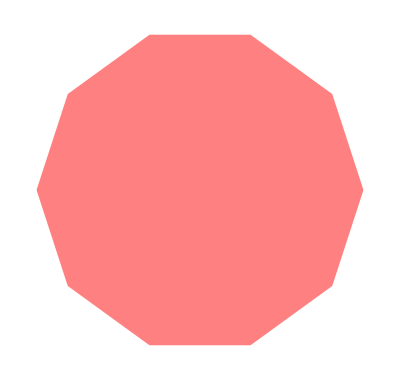

```mathematica
(* 8.6 *) Table[Graphics[Style[RegularPolygon[i],Pink]],{i,5,10}]
```

```mathematica
(* 8.7 *) Graphics3D[Style[Cylinder[],Purple]]
```

-Graphics3D-

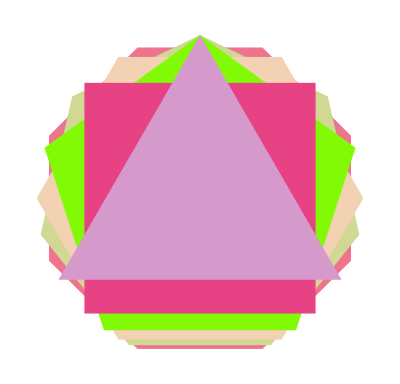

```mathematica
(* 8.8 *) Graphics[Table[
Style[RegularPolygon[i],RandomColor[]],
{i,8,3,-1}
]]
```